```mathematica
f[t_,i0_,j0_,n_]:=Module[{i,j},
Table[
Table[
If[(i==i0&&j==i0)||(i==j0&&j==j0),Cos[t],
If[(i==i0&&j==j0),-Sin[t],
If[(i==j0&&j==i0),Sin[t],
If[i==j,1,0]]]],
{j,1,n}],
{i,1,n}]]
```

```mathematica
r14[t12_,t13_,t14_]:=f[t12,1,2,4].f[t13,1,3,4].f[t14,1,4,4]
```

```mathematica
r24[t12_,t13_,t14_,t23_,t24_]:=r14[t12,t13,t14].f[t23,2,3,4].f[t24,2,4,4]
```

```mathematica
r24[t1,t2,t3,t4,t5]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] | Cos[t5] (-Cos[t4] Sin[t1]-Cos[t1] Sin[t2] Sin[t4])-Cos[t1] Cos[t2] Sin[t3] Sin[t5] | -Cos[t1] Cos[t4] Sin[t2]+Sin[t1] Sin[t4] | -Cos[t1] Cos[t2] Cos[t5] Sin[t3]-(-Cos[t4] Sin[t1]-Cos[t1] Sin[t2] Sin[t4]) Sin[t5]
Cos[t2] Cos[t3] Sin[t1] | Cos[t5] (Cos[t1] Cos[t4]-Sin[t1] Sin[t2] Sin[t4])-Cos[t2] Sin[t1] Sin[t3] Sin[t5] | -Cos[t4] Sin[t1] Sin[t2]-Cos[t1] Sin[t4] | -Cos[t2] Cos[t5] Sin[t1] Sin[t3]-(Cos[t1] Cos[t4]-Sin[t1] Sin[t2] Sin[t4]) Sin[t5]
Cos[t3] Sin[t2] | Cos[t2] Cos[t5] Sin[t4]-Sin[t2] Sin[t3] Sin[t5] | Cos[t2] Cos[t4] | -Cos[t5] Sin[t2] Sin[t3]-Cos[t2] Sin[t4] Sin[t5]
Sin[t3] | Cos[t3] Sin[t5] | 0 | Cos[t3] Cos[t5])

```mathematica
r24[Pi/2,Pi/2,t3,t4,t5]//MatrixForm
```

(0 | -Cos[t4] Cos[t5] | Sin[t4] | Cos[t4] Sin[t5]
0 | -Cos[t5] Sin[t4] | -Cos[t4] | Sin[t4] Sin[t5]
Cos[t3] | -Sin[t3] Sin[t5] | 0 | -Cos[t5] Sin[t3]
Sin[t3] | Cos[t3] Sin[t5] | 0 | Cos[t3] Cos[t5])

```mathematica
r24[Pi/2,Pi/2,t3,Pi/4,t5]//MatrixForm
```

(0 | -Cos[t5]/(√2) | 1/(√2) | Sin[t5]/(√2)
0 | -Cos[t5]/(√2) | -1/(√2) | Sin[t5]/(√2)
Cos[t3] | -Sin[t3] Sin[t5] | 0 | -Cos[t5] Sin[t3]
Sin[t3] | Cos[t3] Sin[t5] | 0 | Cos[t3] Cos[t5])

```mathematica
Plot3D[{Cos[t5]/Sqrt[2],Cos[t3]+Sin[t3]Sin[t5],Sin[t3]+Cos[t3]Sin[t5]},{t3,0,Pi/2},{t5,0,Pi/2},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
r24[Pi/2,Pi/2,Pi/4,Pi/4,t5]//MatrixForm
```

(0 | -Cos[t5]/(√2) | 1/(√2) | Sin[t5]/(√2)
0 | -Cos[t5]/(√2) | -1/(√2) | Sin[t5]/(√2)
1/(√2) | -Sin[t5]/(√2) | 0 | -Cos[t5]/(√2)
1/(√2) | Sin[t5]/(√2) | 0 | Cos[t5]/(√2))

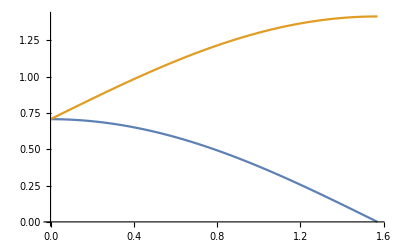

```mathematica
Plot[{Cos[t5]/Sqrt[2],1/Sqrt[2]+Sin[t5]/Sqrt[2]},{t5,0,Pi/2}]
```

```mathematica
r24[Pi/2,Pi/2,Pi/4,Pi/4,0]//MatrixForm
```

(0 | -1/(√2) | 1/(√2) | 0
0 | -1/(√2) | -1/(√2) | 0
1/(√2) | 0 | 0 | -1/(√2)
1/(√2) | 0 | 0 | 1/(√2))

```mathematica
r16[t12_,t13_,t14_,t15_,t16_]:=f[t12,1,2,6].f[t13,1,3,6].f[t14,1,4,6].f[t15,1,5,6].f[t16,1,6,6]
```

```mathematica
r26[t12_,t13_,t14_,t15_,t16_,t23_,t24_,t25_,t26_]:=r16[t12,t13,t14,t15,t16].f[t23,2,3,6].f[t24,2,4,6].f[t25,2,5,6].f[t26,2,6,6]
```

```mathematica
r26[t1,t2,t3,t4,t5,t6,t7,t8,t9]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] | Cos[t9] (Cos[t8] (Cos[t7] (-Cos[t6] Sin[t1]-Cos[t1] Sin[t2] Sin[t6])-Cos[t1] Cos[t2] Sin[t3] Sin[t7])-Cos[t1] Cos[t2] Cos[t3] Sin[t4] Sin[t8])-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t5] Sin[t9] | -Cos[t1] Cos[t6] Sin[t2]+Sin[t1] Sin[t6] | -Cos[t1] Cos[t2] Cos[t7] Sin[t3]-(-Cos[t6] Sin[t1]-Cos[t1] Sin[t2] Sin[t6]) Sin[t7] | -Cos[t1] Cos[t2] Cos[t3] Cos[t8] Sin[t4]-(Cos[t7] (-Cos[t6] Sin[t1]-Cos[t1] Sin[t2] Sin[t6])-Cos[t1] Cos[t2] Sin[t3] Sin[t7]) Sin[t8] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t9] Sin[t5]-(Cos[t8] (Cos[t7] (-Cos[t6] Sin[t1]-Cos[t1] Sin[t2] Sin[t6])-Cos[t1] Cos[t2] Sin[t3] Sin[t7])-Cos[t1] Cos[t2] Cos[t3] Sin[t4] Sin[t8]) Sin[t9]
Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] | Cos[t9] (Cos[t8] (Cos[t7] (Cos[t1] Cos[t6]-Sin[t1] Sin[t2] Sin[t6])-Cos[t2] Sin[t1] Sin[t3] Sin[t7])-Cos[t2] Cos[t3] Sin[t1] Sin[t4] Sin[t8])-Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t5] Sin[t9] | -Cos[t6] Sin[t1] Sin[t2]-Cos[t1] Sin[t6] | -Cos[t2] Cos[t7] Sin[t1] Sin[t3]-(Cos[t1] Cos[t6]-Sin[t1] Sin[t2] Sin[t6]) Sin[t7] | -Cos[t2] Cos[t3] Cos[t8] Sin[t1] Sin[t4]-(Cos[t7] (Cos[t1] Cos[t6]-Sin[t1] Sin[t2] Sin[t6])-Cos[t2] Sin[t1] Sin[t3] Sin[t7]) Sin[t8] | -Cos[t2] Cos[t3] Cos[t4] Cos[t9] Sin[t1] Sin[t5]-(Cos[t8] (Cos[t7] (Cos[t1] Cos[t6]-Sin[t1] Sin[t2] Sin[t6])-Cos[t2] Sin[t1] Sin[t3] Sin[t7])-Cos[t2] Cos[t3] Sin[t1] Sin[t4] Sin[t8]) Sin[t9]
Cos[t3] Cos[t4] Cos[t5] Sin[t2] | Cos[t9] (Cos[t8] (Cos[t2] Cos[t7] Sin[t6]-Sin[t2] Sin[t3] Sin[t7])-Cos[t3] Sin[t2] Sin[t4] Sin[t8])-Cos[t3] Cos[t4] Sin[t2] Sin[t5] Sin[t9] | Cos[t2] Cos[t6] | -Cos[t7] Sin[t2] Sin[t3]-Cos[t2] Sin[t6] Sin[t7] | -Cos[t3] Cos[t8] Sin[t2] Sin[t4]-(Cos[t2] Cos[t7] Sin[t6]-Sin[t2] Sin[t3] Sin[t7]) Sin[t8] | -Cos[t3] Cos[t4] Cos[t9] Sin[t2] Sin[t5]-(Cos[t8] (Cos[t2] Cos[t7] Sin[t6]-Sin[t2] Sin[t3] Sin[t7])-Cos[t3] Sin[t2] Sin[t4] Sin[t8]) Sin[t9]
Cos[t4] Cos[t5] Sin[t3] | Cos[t9] (Cos[t3] Cos[t8] Sin[t7]-Sin[t3] Sin[t4] Sin[t8])-Cos[t4] Sin[t3] Sin[t5] Sin[t9] | 0 | Cos[t3] Cos[t7] | -Cos[t8] Sin[t3] Sin[t4]-Cos[t3] Sin[t7] Sin[t8] | -Cos[t4] Cos[t9] Sin[t3] Sin[t5]-(Cos[t3] Cos[t8] Sin[t7]-Sin[t3] Sin[t4] Sin[t8]) Sin[t9]
Cos[t5] Sin[t4] | Cos[t4] Cos[t9] Sin[t8]-Sin[t4] Sin[t5] Sin[t9] | 0 | 0 | Cos[t4] Cos[t8] | -Cos[t9] Sin[t4] Sin[t5]-Cos[t4] Sin[t8] Sin[t9]
Sin[t5] | Cos[t5] Sin[t9] | 0 | 0 | 0 | Cos[t5] Cos[t9])

```mathematica
r26[Pi/2,Pi/2,t3,t4,t5,t6,t7,t8,t9]//MatrixForm
```

(0 | -Cos[t6] Cos[t7] Cos[t8] Cos[t9] | Sin[t6] | Cos[t6] Sin[t7] | Cos[t6] Cos[t7] Sin[t8] | Cos[t6] Cos[t7] Cos[t8] Sin[t9]
0 | -Cos[t7] Cos[t8] Cos[t9] Sin[t6] | -Cos[t6] | Sin[t6] Sin[t7] | Cos[t7] Sin[t6] Sin[t8] | Cos[t7] Cos[t8] Sin[t6] Sin[t9]
Cos[t3] Cos[t4] Cos[t5] | Cos[t9] (-Cos[t8] Sin[t3] Sin[t7]-Cos[t3] Sin[t4] Sin[t8])-Cos[t3] Cos[t4] Sin[t5] Sin[t9] | 0 | -Cos[t7] Sin[t3] | -Cos[t3] Cos[t8] Sin[t4]+Sin[t3] Sin[t7] Sin[t8] | -Cos[t3] Cos[t4] Cos[t9] Sin[t5]-(-Cos[t8] Sin[t3] Sin[t7]-Cos[t3] Sin[t4] Sin[t8]) Sin[t9]
Cos[t4] Cos[t5] Sin[t3] | Cos[t9] (Cos[t3] Cos[t8] Sin[t7]-Sin[t3] Sin[t4] Sin[t8])-Cos[t4] Sin[t3] Sin[t5] Sin[t9] | 0 | Cos[t3] Cos[t7] | -Cos[t8] Sin[t3] Sin[t4]-Cos[t3] Sin[t7] Sin[t8] | -Cos[t4] Cos[t9] Sin[t3] Sin[t5]-(Cos[t3] Cos[t8] Sin[t7]-Sin[t3] Sin[t4] Sin[t8]) Sin[t9]
Cos[t5] Sin[t4] | Cos[t4] Cos[t9] Sin[t8]-Sin[t4] Sin[t5] Sin[t9] | 0 | 0 | Cos[t4] Cos[t8] | -Cos[t9] Sin[t4] Sin[t5]-Cos[t4] Sin[t8] Sin[t9]
Sin[t5] | Cos[t5] Sin[t9] | 0 | 0 | 0 | Cos[t5] Cos[t9])

```mathematica
r26[Pi/2,Pi/2,t3,t4,t5,t6,t7,t8,0]//MatrixForm
```

(0 | -Cos[t6] Cos[t7] Cos[t8] | Sin[t6] | Cos[t6] Sin[t7] | Cos[t6] Cos[t7] Sin[t8] | 0
0 | -Cos[t7] Cos[t8] Sin[t6] | -Cos[t6] | Sin[t6] Sin[t7] | Cos[t7] Sin[t6] Sin[t8] | 0
Cos[t3] Cos[t4] Cos[t5] | -Cos[t8] Sin[t3] Sin[t7]-Cos[t3] Sin[t4] Sin[t8] | 0 | -Cos[t7] Sin[t3] | -Cos[t3] Cos[t8] Sin[t4]+Sin[t3] Sin[t7] Sin[t8] | -Cos[t3] Cos[t4] Sin[t5]
Cos[t4] Cos[t5] Sin[t3] | Cos[t3] Cos[t8] Sin[t7]-Sin[t3] Sin[t4] Sin[t8] | 0 | Cos[t3] Cos[t7] | -Cos[t8] Sin[t3] Sin[t4]-Cos[t3] Sin[t7] Sin[t8] | -Cos[t4] Sin[t3] Sin[t5]
Cos[t5] Sin[t4] | Cos[t4] Sin[t8] | 0 | 0 | Cos[t4] Cos[t8] | -Sin[t4] Sin[t5]
Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5])

```mathematica
r26[Pi/2,Pi/2,t3,t4,t5,t6,t7,0,0]//MatrixForm
```

(0 | -Cos[t6] Cos[t7] | Sin[t6] | Cos[t6] Sin[t7] | 0 | 0
0 | -Cos[t7] Sin[t6] | -Cos[t6] | Sin[t6] Sin[t7] | 0 | 0
Cos[t3] Cos[t4] Cos[t5] | -Sin[t3] Sin[t7] | 0 | -Cos[t7] Sin[t3] | -Cos[t3] Sin[t4] | -Cos[t3] Cos[t4] Sin[t5]
Cos[t4] Cos[t5] Sin[t3] | Cos[t3] Sin[t7] | 0 | Cos[t3] Cos[t7] | -Sin[t3] Sin[t4] | -Cos[t4] Sin[t3] Sin[t5]
Cos[t5] Sin[t4] | 0 | 0 | 0 | Cos[t4] | -Sin[t4] Sin[t5]
Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5])

```mathematica
r26[Pi/2,Pi/2,Pi/2,t4,t5,Pi/4,t7,0,0]//MatrixForm
```

(0 | -Cos[t7]/(√2) | 1/(√2) | Sin[t7]/(√2) | 0 | 0
0 | -Cos[t7]/(√2) | -1/(√2) | Sin[t7]/(√2) | 0 | 0
0 | -Sin[t7] | 0 | -Cos[t7] | 0 | 0
Cos[t4] Cos[t5] | 0 | 0 | 0 | -Sin[t4] | -Cos[t4] Sin[t5]
Cos[t5] Sin[t4] | 0 | 0 | 0 | Cos[t4] | -Sin[t4] Sin[t5]
Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5])

```mathematica
r26[Pi/2,Pi/2,Pi/2,Pi/4,t5,Pi/4,t7,0,0]//MatrixForm
```

(0 | -Cos[t7]/(√2) | 1/(√2) | Sin[t7]/(√2) | 0 | 0
0 | -Cos[t7]/(√2) | -1/(√2) | Sin[t7]/(√2) | 0 | 0
0 | -Sin[t7] | 0 | -Cos[t7] | 0 | 0
Cos[t5]/(√2) | 0 | 0 | 0 | -1/(√2) | -Sin[t5]/(√2)
Cos[t5]/(√2) | 0 | 0 | 0 | 1/(√2) | -Sin[t5]/(√2)
Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5])

```mathematica
r26[Pi/2,Pi/2,Pi/2,Pi/4,ArcTan[1/Sqrt[2]],Pi/4,ArcTan[1/Sqrt[2]],0,0]//MatrixForm
```

(0 | -1/(√3) | 1/(√2) | 1/(√6) | 0 | 0
0 | -1/(√3) | -1/(√2) | 1/(√6) | 0 | 0
0 | -1/(√3) | 0 | -√(2/3) | 0 | 0
1/(√3) | 0 | 0 | 0 | -1/(√2) | -1/(√6)
1/(√3) | 0 | 0 | 0 | 1/(√2) | -1/(√6)
1/(√3) | 0 | 0 | 0 | 0 | √(2/3))

```mathematica
r18[t12_,t13_,t14_,t15_,t16_,t17_,t18_]:=f[t12,1,2,8].f[t13,1,3,8].f[t14,1,4,8].f[t15,1,5,8].f[t16,1,6,8].f[t17,1,7,8].f[t18,1,8,8]
```

```mathematica
r28[t12_,t13_,t14_,t15_,t16_,t17_,t18_,t23_,t24_,t25_,t26_,t27_,t28_]:=r18[t12,t13,t14,t15,t16,t17,t18].f[t23,2,3,8].f[t24,2,4,8].f[t25,2,5,8].f[t26,2,6,8].f[t27,2,7,8].f[t28,2,8,8]
```

```mathematica
r28[t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13]//MatrixForm
```

(Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] | -Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t13] Sin[t7]+Cos[t13] (-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t12] Sin[t6]+Cos[t12] (-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t1] Cos[t2] Cos[t3] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8])-Cos[t1] Cos[t2] Sin[t3] Sin[t9])))) | -Cos[t1] Cos[t8] Sin[t2]+Sin[t1] Sin[t8] | -Cos[t1] Cos[t2] Cos[t9] Sin[t3]-(-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8]) Sin[t9] | -Cos[t1] Cos[t10] Cos[t2] Cos[t3] Sin[t4]-Sin[t10] (Cos[t9] (-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8])-Cos[t1] Cos[t2] Sin[t3] Sin[t9]) | -Cos[t1] Cos[t11] Cos[t2] Cos[t3] Cos[t4] Sin[t5]-Sin[t11] (-Cos[t1] Cos[t2] Cos[t3] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8])-Cos[t1] Cos[t2] Sin[t3] Sin[t9])) | -Cos[t1] Cos[t12] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t6]-Sin[t12] (-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t1] Cos[t2] Cos[t3] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8])-Cos[t1] Cos[t2] Sin[t3] Sin[t9]))) | -Cos[t1] Cos[t13] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t7]-Sin[t13] (-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t12] Sin[t6]+Cos[t12] (-Cos[t1] Cos[t2] Cos[t3] Cos[t4] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t1] Cos[t2] Cos[t3] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (-Cos[t8] Sin[t1]-Cos[t1] Sin[t2] Sin[t8])-Cos[t1] Cos[t2] Sin[t3] Sin[t9]))))
Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t1] | -Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t1] Sin[t13] Sin[t7]+Cos[t13] (-Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] Sin[t12] Sin[t6]+Cos[t12] (-Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t2] Cos[t3] Sin[t1] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8])-Cos[t2] Sin[t1] Sin[t3] Sin[t9])))) | -Cos[t8] Sin[t1] Sin[t2]-Cos[t1] Sin[t8] | -Cos[t2] Cos[t9] Sin[t1] Sin[t3]-(Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8]) Sin[t9] | -Cos[t10] Cos[t2] Cos[t3] Sin[t1] Sin[t4]-Sin[t10] (Cos[t9] (Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8])-Cos[t2] Sin[t1] Sin[t3] Sin[t9]) | -Cos[t11] Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t5]-Sin[t11] (-Cos[t2] Cos[t3] Sin[t1] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8])-Cos[t2] Sin[t1] Sin[t3] Sin[t9])) | -Cos[t12] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] Sin[t6]-Sin[t12] (-Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t2] Cos[t3] Sin[t1] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8])-Cos[t2] Sin[t1] Sin[t3] Sin[t9]))) | -Cos[t13] Cos[t2] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t1] Sin[t7]-Sin[t13] (-Cos[t2] Cos[t3] Cos[t4] Cos[t5] Sin[t1] Sin[t12] Sin[t6]+Cos[t12] (-Cos[t2] Cos[t3] Cos[t4] Sin[t1] Sin[t11] Sin[t5]+Cos[t11] (-Cos[t2] Cos[t3] Sin[t1] Sin[t10] Sin[t4]+Cos[t10] (Cos[t9] (Cos[t1] Cos[t8]-Sin[t1] Sin[t2] Sin[t8])-Cos[t2] Sin[t1] Sin[t3] Sin[t9]))))
Cos[t3] Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t2] | -Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t13] Sin[t2] Sin[t7]+Cos[t13] (-Cos[t3] Cos[t4] Cos[t5] Sin[t12] Sin[t2] Sin[t6]+Cos[t12] (-Cos[t3] Cos[t4] Sin[t11] Sin[t2] Sin[t5]+Cos[t11] (-Cos[t3] Sin[t10] Sin[t2] Sin[t4]+Cos[t10] (Cos[t2] Cos[t9] Sin[t8]-Sin[t2] Sin[t3] Sin[t9])))) | Cos[t2] Cos[t8] | -Cos[t9] Sin[t2] Sin[t3]-Cos[t2] Sin[t8] Sin[t9] | -Cos[t10] Cos[t3] Sin[t2] Sin[t4]-Sin[t10] (Cos[t2] Cos[t9] Sin[t8]-Sin[t2] Sin[t3] Sin[t9]) | -Cos[t11] Cos[t3] Cos[t4] Sin[t2] Sin[t5]-Sin[t11] (-Cos[t3] Sin[t10] Sin[t2] Sin[t4]+Cos[t10] (Cos[t2] Cos[t9] Sin[t8]-Sin[t2] Sin[t3] Sin[t9])) | -Cos[t12] Cos[t3] Cos[t4] Cos[t5] Sin[t2] Sin[t6]-Sin[t12] (-Cos[t3] Cos[t4] Sin[t11] Sin[t2] Sin[t5]+Cos[t11] (-Cos[t3] Sin[t10] Sin[t2] Sin[t4]+Cos[t10] (Cos[t2] Cos[t9] Sin[t8]-Sin[t2] Sin[t3] Sin[t9]))) | -Cos[t13] Cos[t3] Cos[t4] Cos[t5] Cos[t6] Sin[t2] Sin[t7]-Sin[t13] (-Cos[t3] Cos[t4] Cos[t5] Sin[t12] Sin[t2] Sin[t6]+Cos[t12] (-Cos[t3] Cos[t4] Sin[t11] Sin[t2] Sin[t5]+Cos[t11] (-Cos[t3] Sin[t10] Sin[t2] Sin[t4]+Cos[t10] (Cos[t2] Cos[t9] Sin[t8]-Sin[t2] Sin[t3] Sin[t9]))))
Cos[t4] Cos[t5] Cos[t6] Cos[t7] Sin[t3] | -Cos[t4] Cos[t5] Cos[t6] Sin[t13] Sin[t3] Sin[t7]+Cos[t13] (-Cos[t4] Cos[t5] Sin[t12] Sin[t3] Sin[t6]+Cos[t12] (-Cos[t4] Sin[t11] Sin[t3] Sin[t5]+Cos[t11] (-Sin[t10] Sin[t3] Sin[t4]+Cos[t10] Cos[t3] Sin[t9]))) | 0 | Cos[t3] Cos[t9] | -Cos[t10] Sin[t3] Sin[t4]-Cos[t3] Sin[t10] Sin[t9] | -Cos[t11] Cos[t4] Sin[t3] Sin[t5]-Sin[t11] (-Sin[t10] Sin[t3] Sin[t4]+Cos[t10] Cos[t3] Sin[t9]) | -Cos[t12] Cos[t4] Cos[t5] Sin[t3] Sin[t6]-Sin[t12] (-Cos[t4] Sin[t11] Sin[t3] Sin[t5]+Cos[t11] (-Sin[t10] Sin[t3] Sin[t4]+Cos[t10] Cos[t3] Sin[t9])) | -Cos[t13] Cos[t4] Cos[t5] Cos[t6] Sin[t3] Sin[t7]-Sin[t13] (-Cos[t4] Cos[t5] Sin[t12] Sin[t3] Sin[t6]+Cos[t12] (-Cos[t4] Sin[t11] Sin[t3] Sin[t5]+Cos[t11] (-Sin[t10] Sin[t3] Sin[t4]+Cos[t10] Cos[t3] Sin[t9])))
Cos[t5] Cos[t6] Cos[t7] Sin[t4] | Cos[t13] (Cos[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t5] Sin[t12] Sin[t4] Sin[t6])-Cos[t5] Cos[t6] Sin[t13] Sin[t4] Sin[t7] | 0 | 0 | Cos[t10] Cos[t4] | -Cos[t4] Sin[t10] Sin[t11]-Cos[t11] Sin[t4] Sin[t5] | -Sin[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t12] Cos[t5] Sin[t4] Sin[t6] | -Sin[t13] (Cos[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t5] Sin[t12] Sin[t4] Sin[t6])-Cos[t13] Cos[t5] Cos[t6] Sin[t4] Sin[t7]
Cos[t6] Cos[t7] Sin[t5] | Cos[t13] (Cos[t12] Cos[t5] Sin[t11]-Sin[t12] Sin[t5] Sin[t6])-Cos[t6] Sin[t13] Sin[t5] Sin[t7] | 0 | 0 | 0 | Cos[t11] Cos[t5] | -Cos[t5] Sin[t11] Sin[t12]-Cos[t12] Sin[t5] Sin[t6] | -Sin[t13] (Cos[t12] Cos[t5] Sin[t11]-Sin[t12] Sin[t5] Sin[t6])-Cos[t13] Cos[t6] Sin[t5] Sin[t7]
Cos[t7] Sin[t6] | Cos[t13] Cos[t6] Sin[t12]-Sin[t13] Sin[t6] Sin[t7] | 0 | 0 | 0 | 0 | Cos[t12] Cos[t6] | -Cos[t6] Sin[t12] Sin[t13]-Cos[t13] Sin[t6] Sin[t7]
Sin[t7] | Cos[t7] Sin[t13] | 0 | 0 | 0 | 0 | 0 | Cos[t13] Cos[t7])

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13]//MatrixForm
```

(0 | -Cos[t10] Cos[t11] Cos[t12] Cos[t13] Cos[t8] Cos[t9] | Sin[t8] | Cos[t8] Sin[t9] | Cos[t8] Cos[t9] Sin[t10] | Cos[t10] Cos[t8] Cos[t9] Sin[t11] | Cos[t10] Cos[t11] Cos[t8] Cos[t9] Sin[t12] | Cos[t10] Cos[t11] Cos[t12] Cos[t8] Cos[t9] Sin[t13]
0 | -Cos[t10] Cos[t11] Cos[t12] Cos[t13] Cos[t9] Sin[t8] | -Cos[t8] | Sin[t8] Sin[t9] | Cos[t9] Sin[t10] Sin[t8] | Cos[t10] Cos[t9] Sin[t11] Sin[t8] | Cos[t10] Cos[t11] Cos[t9] Sin[t12] Sin[t8] | Cos[t10] Cos[t11] Cos[t12] Cos[t9] Sin[t13] Sin[t8]
0 | -Cos[t10] Cos[t11] Cos[t12] Cos[t13] Sin[t9] | 0 | -Cos[t9] | Sin[t10] Sin[t9] | Cos[t10] Sin[t11] Sin[t9] | Cos[t10] Cos[t11] Sin[t12] Sin[t9] | Cos[t10] Cos[t11] Cos[t12] Sin[t13] Sin[t9]
Cos[t4] Cos[t5] Cos[t6] Cos[t7] | Cos[t13] (Cos[t12] (-Cos[t11] Sin[t10] Sin[t4]-Cos[t4] Sin[t11] Sin[t5])-Cos[t4] Cos[t5] Sin[t12] Sin[t6])-Cos[t4] Cos[t5] Cos[t6] Sin[t13] Sin[t7] | 0 | 0 | -Cos[t10] Sin[t4] | Sin[t10] Sin[t11] Sin[t4]-Cos[t11] Cos[t4] Sin[t5] | -Sin[t12] (-Cos[t11] Sin[t10] Sin[t4]-Cos[t4] Sin[t11] Sin[t5])-Cos[t12] Cos[t4] Cos[t5] Sin[t6] | -Sin[t13] (Cos[t12] (-Cos[t11] Sin[t10] Sin[t4]-Cos[t4] Sin[t11] Sin[t5])-Cos[t4] Cos[t5] Sin[t12] Sin[t6])-Cos[t13] Cos[t4] Cos[t5] Cos[t6] Sin[t7]
Cos[t5] Cos[t6] Cos[t7] Sin[t4] | Cos[t13] (Cos[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t5] Sin[t12] Sin[t4] Sin[t6])-Cos[t5] Cos[t6] Sin[t13] Sin[t4] Sin[t7] | 0 | 0 | Cos[t10] Cos[t4] | -Cos[t4] Sin[t10] Sin[t11]-Cos[t11] Sin[t4] Sin[t5] | -Sin[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t12] Cos[t5] Sin[t4] Sin[t6] | -Sin[t13] (Cos[t12] (Cos[t11] Cos[t4] Sin[t10]-Sin[t11] Sin[t4] Sin[t5])-Cos[t5] Sin[t12] Sin[t4] Sin[t6])-Cos[t13] Cos[t5] Cos[t6] Sin[t4] Sin[t7]
Cos[t6] Cos[t7] Sin[t5] | Cos[t13] (Cos[t12] Cos[t5] Sin[t11]-Sin[t12] Sin[t5] Sin[t6])-Cos[t6] Sin[t13] Sin[t5] Sin[t7] | 0 | 0 | 0 | Cos[t11] Cos[t5] | -Cos[t5] Sin[t11] Sin[t12]-Cos[t12] Sin[t5] Sin[t6] | -Sin[t13] (Cos[t12] Cos[t5] Sin[t11]-Sin[t12] Sin[t5] Sin[t6])-Cos[t13] Cos[t6] Sin[t5] Sin[t7]
Cos[t7] Sin[t6] | Cos[t13] Cos[t6] Sin[t12]-Sin[t13] Sin[t6] Sin[t7] | 0 | 0 | 0 | 0 | Cos[t12] Cos[t6] | -Cos[t6] Sin[t12] Sin[t13]-Cos[t13] Sin[t6] Sin[t7]
Sin[t7] | Cos[t7] Sin[t13] | 0 | 0 | 0 | 0 | 0 | Cos[t13] Cos[t7])

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,t5,t6,t7,t8,t9,t10,0,0,0]//MatrixForm
```

(0 | -Cos[t10] Cos[t8] Cos[t9] | Sin[t8] | Cos[t8] Sin[t9] | Cos[t8] Cos[t9] Sin[t10] | 0 | 0 | 0
0 | -Cos[t10] Cos[t9] Sin[t8] | -Cos[t8] | Sin[t8] Sin[t9] | Cos[t9] Sin[t10] Sin[t8] | 0 | 0 | 0
0 | -Cos[t10] Sin[t9] | 0 | -Cos[t9] | Sin[t10] Sin[t9] | 0 | 0 | 0
Cos[t4] Cos[t5] Cos[t6] Cos[t7] | -Sin[t10] Sin[t4] | 0 | 0 | -Cos[t10] Sin[t4] | -Cos[t4] Sin[t5] | -Cos[t4] Cos[t5] Sin[t6] | -Cos[t4] Cos[t5] Cos[t6] Sin[t7]
Cos[t5] Cos[t6] Cos[t7] Sin[t4] | Cos[t4] Sin[t10] | 0 | 0 | Cos[t10] Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6] | -Cos[t5] Cos[t6] Sin[t4] Sin[t7]
Cos[t6] Cos[t7] Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6] | -Cos[t6] Sin[t5] Sin[t7]
Cos[t7] Sin[t6] | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6] Sin[t7]
Sin[t7] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t7])

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,t5,t6,t7,Pi/4,t9,t10,0,0,0]//MatrixForm
```

(0 | -(Cos[t10] Cos[t9])/(√2) | 1/(√2) | Sin[t9]/(√2) | (Cos[t9] Sin[t10])/(√2) | 0 | 0 | 0
0 | -(Cos[t10] Cos[t9])/(√2) | -1/(√2) | Sin[t9]/(√2) | (Cos[t9] Sin[t10])/(√2) | 0 | 0 | 0
0 | -Cos[t10] Sin[t9] | 0 | -Cos[t9] | Sin[t10] Sin[t9] | 0 | 0 | 0
Cos[t4] Cos[t5] Cos[t6] Cos[t7] | -Sin[t10] Sin[t4] | 0 | 0 | -Cos[t10] Sin[t4] | -Cos[t4] Sin[t5] | -Cos[t4] Cos[t5] Sin[t6] | -Cos[t4] Cos[t5] Cos[t6] Sin[t7]
Cos[t5] Cos[t6] Cos[t7] Sin[t4] | Cos[t4] Sin[t10] | 0 | 0 | Cos[t10] Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6] | -Cos[t5] Cos[t6] Sin[t4] Sin[t7]
Cos[t6] Cos[t7] Sin[t5] | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6] | -Cos[t6] Sin[t5] Sin[t7]
Cos[t7] Sin[t6] | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6] Sin[t7]
Sin[t7] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[t7])

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,t5,t6,ArcTan[Sin[t6]],Pi/4,t9,t10,0,0,0]//MatrixForm
```

(0 | -(Cos[t10] Cos[t9])/(√2) | 1/(√2) | Sin[t9]/(√2) | (Cos[t9] Sin[t10])/(√2) | 0 | 0 | 0
0 | -(Cos[t10] Cos[t9])/(√2) | -1/(√2) | Sin[t9]/(√2) | (Cos[t9] Sin[t10])/(√2) | 0 | 0 | 0
0 | -Cos[t10] Sin[t9] | 0 | -Cos[t9] | Sin[t10] Sin[t9] | 0 | 0 | 0
(Cos[t4] Cos[t5] Cos[t6])/(√(1+Sin[t6]^2)) | -Sin[t10] Sin[t4] | 0 | 0 | -Cos[t10] Sin[t4] | -Cos[t4] Sin[t5] | -Cos[t4] Cos[t5] Sin[t6] | -(Cos[t4] Cos[t5] Cos[t6] Sin[t6])/(√(1+Sin[t6]^2))
(Cos[t5] Cos[t6] Sin[t4])/(√(1+Sin[t6]^2)) | Cos[t4] Sin[t10] | 0 | 0 | Cos[t10] Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6] | -(Cos[t5] Cos[t6] Sin[t4] Sin[t6])/(√(1+Sin[t6]^2))
(Cos[t6] Sin[t5])/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6] | -(Cos[t6] Sin[t5] Sin[t6])/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√(1+Sin[t6]^2)))

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,t5,t6,ArcTan[Sin[t6]],Pi/4,ArcTan[1/Sqrt[2]],t10,0,0,0]//MatrixForm
```

(0 | -Cos[t10]/(√3) | 1/(√2) | 1/(√6) | Sin[t10]/(√3) | 0 | 0 | 0
0 | -Cos[t10]/(√3) | -1/(√2) | 1/(√6) | Sin[t10]/(√3) | 0 | 0 | 0
0 | -Cos[t10]/(√3) | 0 | -√(2/3) | Sin[t10]/(√3) | 0 | 0 | 0
(Cos[t4] Cos[t5] Cos[t6])/(√(1+Sin[t6]^2)) | -Sin[t10] Sin[t4] | 0 | 0 | -Cos[t10] Sin[t4] | -Cos[t4] Sin[t5] | -Cos[t4] Cos[t5] Sin[t6] | -(Cos[t4] Cos[t5] Cos[t6] Sin[t6])/(√(1+Sin[t6]^2))
(Cos[t5] Cos[t6] Sin[t4])/(√(1+Sin[t6]^2)) | Cos[t4] Sin[t10] | 0 | 0 | Cos[t10] Cos[t4] | -Sin[t4] Sin[t5] | -Cos[t5] Sin[t4] Sin[t6] | -(Cos[t5] Cos[t6] Sin[t4] Sin[t6])/(√(1+Sin[t6]^2))
(Cos[t6] Sin[t5])/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | Cos[t5] | -Sin[t5] Sin[t6] | -(Cos[t6] Sin[t5] Sin[t6])/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√(1+Sin[t6]^2)))

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,ArcSin[Tan[t6]],t6,ArcTan[Sin[t6]],Pi/4,ArcTan[1/Sqrt[2]],t10,0,0,0]//MatrixForm
```

(0 | -Cos[t10]/(√3) | 1/(√2) | 1/(√6) | Sin[t10]/(√3) | 0 | 0 | 0
0 | -Cos[t10]/(√3) | -1/(√2) | 1/(√6) | Sin[t10]/(√3) | 0 | 0 | 0
0 | -Cos[t10]/(√3) | 0 | -√(2/3) | Sin[t10]/(√3) | 0 | 0 | 0
(Cos[t4] Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2)) | -Sin[t10] Sin[t4] | 0 | 0 | -Cos[t10] Sin[t4] | -Cos[t4] Tan[t6] | -Cos[t4] Sin[t6] √(1-Tan[t6]^2) | -(Cos[t4] Cos[t6] Sin[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))
(Cos[t6] Sin[t4] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2)) | Cos[t4] Sin[t10] | 0 | 0 | Cos[t10] Cos[t4] | -Sin[t4] Tan[t6] | -Sin[t4] Sin[t6] √(1-Tan[t6]^2) | -(Cos[t6] Sin[t4] Sin[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | √(1-Tan[t6]^2) | -Sin[t6] Tan[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√(1+Sin[t6]^2)))

```mathematica
r28[Pi/2,Pi/2,Pi/2,t4,ArcSin[Tan[t6]],t6,ArcTan[Sin[t6]],Pi/4,ArcTan[1/Sqrt[2]],ArcCos[Sqrt[3] Sin[t6]/(√(1+Sin[t6]^2))],0,0,0]//MatrixForm
```

(0 | -Sin[t6]/(√(1+Sin[t6]^2)) | 1/(√2) | 1/(√6) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
0 | -Sin[t6]/(√(1+Sin[t6]^2)) | -1/(√2) | 1/(√6) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
0 | -Sin[t6]/(√(1+Sin[t6]^2)) | 0 | -√(2/3) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
(Cos[t4] Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2)) | -Sin[t4] √(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)) | 0 | 0 | -(√3 Sin[t4] Sin[t6])/(√(1+Sin[t6]^2)) | -Cos[t4] Tan[t6] | -Cos[t4] Sin[t6] √(1-Tan[t6]^2) | -(Cos[t4] Cos[t6] Sin[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))
(Cos[t6] Sin[t4] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2)) | Cos[t4] √(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)) | 0 | 0 | (√3 Cos[t4] Sin[t6])/(√(1+Sin[t6]^2)) | -Sin[t4] Tan[t6] | -Sin[t4] Sin[t6] √(1-Tan[t6]^2) | -(Cos[t6] Sin[t4] Sin[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | √(1-Tan[t6]^2) | -Sin[t6] Tan[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√(1+Sin[t6]^2)))

```mathematica
FullSimplify[(Cos[t4] Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))+Sin[t4] √(1-(3 Sin[t6]^2)/(1+Sin[t6]^2))]
```

Sin[t4] √(Cos[2 t6]/(1+Sin[t6]^2))+(Cos[t4] Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))

```mathematica
FullSimplify[(Cos[t6] Sin[t4] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))+Cos[t4] √(1-(3 Sin[t6]^2)/(1+Sin[t6]^2))]
```

Cos[t4] √(Cos[2 t6]/(1+Sin[t6]^2))+(Cos[t6] Sin[t4] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))

```mathematica
r28[Pi/2,Pi/2,Pi/2,Pi/2,ArcSin[Tan[t6]],t6,ArcTan[Sin[t6]],Pi/4,ArcTan[1/Sqrt[2]],ArcCos[Sqrt[3] Sin[t6]/(√(1+Sin[t6]^2))],0,0,0]//MatrixForm
```

(0 | -Sin[t6]/(√(1+Sin[t6]^2)) | 1/(√2) | 1/(√6) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
0 | -Sin[t6]/(√(1+Sin[t6]^2)) | -1/(√2) | 1/(√6) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
0 | -Sin[t6]/(√(1+Sin[t6]^2)) | 0 | -√(2/3) | (√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)))/(√3) | 0 | 0 | 0
0 | -√(1-(3 Sin[t6]^2)/(1+Sin[t6]^2)) | 0 | 0 | -(√3 Sin[t6])/(√(1+Sin[t6]^2)) | 0 | 0 | 0
(Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | -Tan[t6] | -Sin[t6] √(1-Tan[t6]^2) | -(Cos[t6] Sin[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | √(1-Tan[t6]^2) | -Sin[t6] Tan[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | Cos[t6] | -Sin[t6]^2/(√(1+Sin[t6]^2))
Sin[t6]/(√(1+Sin[t6]^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 1/(√(1+Sin[t6]^2)))

```mathematica
Solve[(Cos[t6] √(1-Tan[t6]^2))/(√(1+Sin[t6]^2))==Sin[t6]/(√(1+Sin[t6]^2)),t6]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t6→-ArcCos[-√(2/3)]},{t6→ArcCos[√(2/3)]}}

```mathematica
r28[Pi/2,Pi/2,Pi/2,Pi/2,ArcSin[Tan[t6]],t6,ArcTan[Sin[t6]],Pi/4,ArcTan[1/Sqrt[2]],ArcCos[Sqrt[3] Sin[t6]/(√(1+Sin[t6]^2))],0,0,0]/.t6->ArcCos[√(2/3)]//MatrixForm
```

(0 | -1/2 | 1/(√2) | 1/(√6) | 1/(2 √3) | 0 | 0 | 0
0 | -1/2 | -1/(√2) | 1/(√6) | 1/(2 √3) | 0 | 0 | 0
0 | -1/2 | 0 | -√(2/3) | 1/(2 √3) | 0 | 0 | 0
0 | -1/2 | 0 | 0 | -(√3)/2 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | -1/(√2) | -1/(√6) | -1/(2 √3)
1/2 | 0 | 0 | 0 | 0 | 1/(√2) | -1/(√6) | -1/(2 √3)
1/2 | 0 | 0 | 0 | 0 | 0 | √(2/3) | -1/(2 √3)
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | (√3)/2)